First we input the story as text:

```mathematica
corpus:="In ‘Macbeth’, Shakespeare uses the theme, ambition as a driving force throughout the play. He calls on ambition as a motivation for characters to strive for power, or kill for the throne. Ambition is initiated in Act 1, when Macbeth has an unusual reaction to the witches prophecy. It is then developed throughout the play with Lady Macbeth, and brutally resolved in Act 5, with Macbeth’s head on a stake.

Macbeth’s ambition is sparked in Act 1, when the witches intrigue him with a twisted prophecy. “Thane of Glamis/ Thane of Cawdor/ and shall be king hereafter!”. Since Macbeth is already thane of Glamis, then later given the title, Thane of Cawdor, he practically expects to be the king. Macbeth’s reaction to the prophecy was odd, because at the time the play was written, society was very sceptical of witchcraft, though Macbeth talked to the witches almost as if they were equal. This is the first of Macbeth’s ambition in the play, but later, Shakespeare uses it as a driving force.

Macbeth’s ambition, although determined, holds much more reason and patience until Lady Macbeth manipulates him into possessing a need to be king. She even purposely identifies her weakness and sacrifices it to spirit, which is one of her turning points in the play. She screams “replace my milk with gall”, which is Lady Macbeth asking for her femininity to be replaced with cold hearted ambition. It is evidence that the play displays the destructive power of ambition.

“Fair is Foul, and Foul is Fair.” This motif is taken from early in the play, and is a suggestion that not only is there little distinction between good and bad, bad, but that all sins against the great chain of being will be reversed. And so it was. Ever since Macbeth killed the king, everything he had came spiralling downwards. Even just after the murder , Lady Macbeth would “hate to wear hands as pale as yours”, a symbol of mistrust between the couple, whose relationship ends with a tragedy, and is the final result of their ambition.

Macbeth contains broad symbols, visual images and motifs to describe the ultimate and seemingly infinitely powerful driving force of ambition in the play, and is relentlessly resolved with a terrible ending."
```

### Analysis

#### Counting words

Simply counting the words, and what kinds of words, can be useful.

```mathematica
Print["Number of words:"]; WordCount[corpus]
words:=ToLowerCase[StringSplit[corpus, Except[WordCharacter]..]]
sentences:=TextSentences[corpus]
Print["Number of distinct words: "];
CountDistinct[words]
```

Number of words:

377

Number of distinct words:

189

Using the two above, we can create a measure of the vocabularly variety, by dividing the distinct words by the total words, we get a measure from 0 to 1 of the word variation. 1 being every single word is different.

```mathematica
Print["Vocab density: "];CountDistinct[words]/Length[words]//N
```

Vocab density:

0.494764

We can also remove words such as “then”, “this”, “and”, known as stop words, and then repeat the vocab density calculation. This should be a larger number more often than not.

```mathematica
trimmedWords:=DeleteStopwords[words];
Print["Vocab density, without stop words: "];CountDistinct[trimmedWords]/Length[trimmedWords]//N
```

Vocab density, without stop words:

0.666667

```mathematica
Print["The 20 most commonly used words:"];Take[WordCounts[DeleteStopwords[corpus]],20]
```

The 20 most commonly used words:

<|Macbeth→15,ambition→9,play→8,Lady→4,king→4,witches→3,Thane→3,prophecy→3,force→3,driving→3,Act→3,uses→2,throughout→2,Shakespeare→2,resolved→2,reaction→2,power→2,later→2,Glamis→2,Foul→2|>

We can also look at the density of certain types of words, for example:

```mathematica
Print["Density of adjectives:"];
Length[Intersection[WordList["Adjective"],trimmedWords]]/Length[trimmedWords]//N
```

Density of adjectives:

0.163934

Note that the above example may count words as adjectives when they are not being used as such in a sentence, however it should be good enough for a rough measure.

### Sentence length

We can also look at the sentece length throughout the text

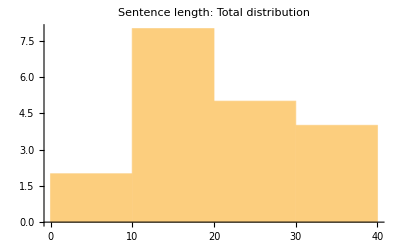

```mathematica
sentenceLengths:=Length/@StringSplit/@sentences;
Histogram[sentenceLengths, PlotLabel->"Sentence length: Total distribution"]
```

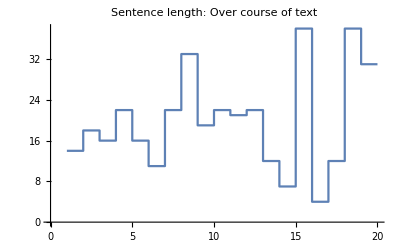

```mathematica
ListStepPlot[sentenceLengths, PlotLabel->"Sentence length: Over course of text"]
```

We can also look at the mean of the absolute value of the second differences of the sentence length as a measure of the variability of the sentence lengths throughout the text. This gives us a sense of how much short sentences follow long ones (higher being more variation)

17.7059

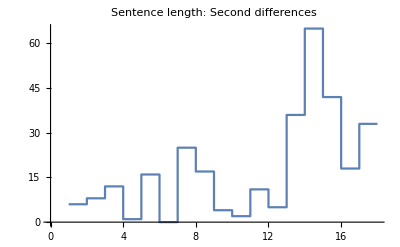

```mathematica
Mean[Abs/@Differences[sentenceLengths,2]]//N
ListStepPlot[Interpolation[Abs/@Differences[sentenceLengths,2]], PlotLabel->"Sentence length: Second differences"]
```

We can also drill down into the individual sentence structure itself

```mathematica
TextStructure[sentences[[4]]]
```

It
Pronoun
Noun Phrase  is
Verb  then
Adverb
Adverb Phrase    developed
Verb  throughout
Preposition    the
Determinerplay
Noun
Noun Phrase  with
Preposition  Lady
Proper NounMacbeth
Proper Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Verb Phrase,
Punctuationand
Conjunction  brutally
Adverb
Adverb Phrase  resolved
Verb  in
Preposition  Act
Proper Noun5
Numeral
Noun Phrase
Prepositional Phrase,
Punctuation  with
Preposition      Macbeth
Proper Noun's
Missing[KeyAbsent,Nothing]
Noun Phrasehead
Noun
Noun Phrase  on
Preposition  a
Determinerstake
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence